## A small branched pathway example.

## First introduce the steady state equations, and find the MSS map x0=F(z;x2,x5)

```mathematica
eqs={z1 (x0-x1)/(a1+b1 x0+c1 x1)==1,
z2(x2-x3)/(a2+b2 x2+c2 x3)==1,
z3(x1 x3 - x4)/(a3+ b3 x1 x3+c3 x4)==1,
z4(x4-x5)/(a4+b4 x4+c4 x5)==1}
xs=Solve[eqs,{x0,x1,x3,x4}]//FullSimplify
F=x0/.xs[[1]][[1]]//Factor
```

{((x0-x1) z1)/(a1+b1 x0+c1 x1)==1,((x2-x3) z2)/(a2+b2 x2+c2 x3)==1,((x1 x3-x4) z3)/(a3+b3 x1 x3+c3 x4)==1,((x4-x5) z4)/(a4+b4 x4+c4 x5)==1}

{{x0→(-a1+((c1+z1) (c2+z2) (a3 (-b4+z4)+(c3+z3) (a4+x5 (c4+z4))))/((a2+x2 (b2-z2)) (b3-z3) (b4-z4)))/(b1-z1),x1→-((c2+z2) (a3 (-b4+z4)+(c3+z3) (a4+x5 (c4+z4))))/((a2+x2 (b2-z2)) (b3-z3) (b4-z4)),x3→-(a2+b2 x2-x2 z2)/(c2+z2),x4→-(a4+x5 (c4+z4))/(b4-z4)}}

(-a1 a2 b3 b4-a3 b4 c1 c2+a4 c1 c2 c3-a1 b2 b3 b4 x2+c1 c2 c3 c4 x5-a3 b4 c2 z1+a4 c2 c3 z1+c2 c3 c4 x5 z1-a3 b4 c1 z2+a4 c1 c3 z2+a1 b3 b4 x2 z2+c1 c3 c4 x5 z2-a3 b4 z1 z2+a4 c3 z1 z2+c3 c4 x5 z1 z2+a1 a2 b4 z3+a4 c1 c2 z3+a1 b2 b4 x2 z3+c1 c2 c4 x5 z3+a4 c2 z1 z3+c2 c4 x5 z1 z3+a4 c1 z2 z3-a1 b4 x2 z2 z3+c1 c4 x5 z2 z3+a4 z1 z2 z3+c4 x5 z1 z2 z3+a1 a2 b3 z4+a3 c1 c2 z4+a1 b2 b3 x2 z4+c1 c2 c3 x5 z4+a3 c2 z1 z4+c2 c3 x5 z1 z4+a3 c1 z2 z4-a1 b3 x2 z2 z4+c1 c3 x5 z2 z4+a3 z1 z2 z4+c3 x5 z1 z2 z4-a1 a2 z3 z4-a1 b2 x2 z3 z4+c1 c2 x5 z3 z4+c2 x5 z1 z3 z4+a1 x2 z2 z3 z4+c1 x5 z2 z3 z4+x5 z1 z2 z3 z4)/((b1-z1) (a2+b2 x2-x2 z2) (b3-z3) (b4-z4))

```mathematica
Solve[- t2==(a2+b2 x2-x2 z2),z2]
```

{{z2→(a2+t2+b2 x2)/x2}}

```mathematica
repl={z1->t1-b1,z2->(a2+t2+b2 x2)/x2,z3->t3-b3,z4->t4-b4};
(**repl={z1->b1-t1,z3->b3-t3,z4->b4-t4};**)
D[F,z1]/.repl//FullSimplify
D[F,z2]/.repl//FullSimplify
D[F,z3]/.repl//FullSimplify
D[F,z4]/.repl//FullSimplify
```

(a4 (b1+c1) (b3-c3-t3) (t2+(b2+c2) x2)+(2 b4-t4) (a1 t2 (-2 b3+t3) x2+a3 (b1+c1) (t2+(b2+c2) x2))-(b1+c1) (b3-c3-t3) (b4-c4-t4) (t2+(b2+c2) x2) x5+a2 (b1+c1) (a3 (2 b4-t4)+(b3-c3-t3) (a4+(-b4+c4+t4) x5)))/((-2 b1+t1)^2 t2 (2 b3-t3) (2 b4-t4) x2)

-((b1-c1-t1) (a2+(b2+c2) x2) (a3 (-2 b4+t4)-(b3-c3-t3) (a4+(-b4+c4+t4) x5)))/((2 b1-t1) t2^2 (2 b3-t3) (2 b4-t4))

((b1-c1-t1) (a2+t2+(b2+c2) x2) (a3 (-2 b4+t4)+(b3+c3) (a4+(-b4+c4+t4) x5)))/((2 b1-t1) t2 (-2 b3+t3)^2 (2 b4-t4) x2)

-((b1-c1-t1) (b3-c3-t3) (a2+t2+(b2+c2) x2) (a4+(b4+c4) x5))/((2 b1-t1) t2 (2 b3-t3) (-2 b4+t4)^2 x2)

## Compute the Hessian of F wrt z, and find its determinant

```mathematica
H={{D[D[F,z1],z1],D[D[F,z1],z2],D[D[F,z1],z3],D[D[F,z1],z4]},
{D[D[F,z2],z1],D[D[F,z2],z2],D[D[F,z2],z3],D[D[F,z2],z4]},
{D[D[F,z3],z1],D[D[F,z3],z2],D[D[F,z3],z3],D[D[F,z3],z4]},
{D[D[F,z4],z1],D[D[F,z4],z2],D[D[F,z4],z3],D[D[F,z4],z4]}}//FullSimplify;
```

```mathematica
detH=Det[H]/.{d3->0,e3->0}/.repl // Factor;
Length[detH]
```

10

```mathematica
repl={z1->t1+c1,z2->t2+c2 ,z3->t3+c3,z4->t4+c4};(x5/.xs//Factor//Denominator)/.repl//Factor
```

{1}

## Replace the z variables by new ones that are always positive on the domain of F, compute Denom and Numer of det[H] and notice that both are always positive.

```mathematica
repl={z1->t1-c1,z2->t2-c2 ,z3->t3-c3,z4->t4-c4};
detH//Numerator/.repl;
(x5/.xs//Factor//Numerator)/.repl//Expand;
(x5/.xs//Factor//Denominator)/.repl//Factor;
```

## Check the positivity of the eigenvalues for one concrete example to conclude that they are positive for all parameter choices

```mathematica
Hconcrete=(H/.repl)/.{
a1->1,a2->1,a3->1,a4->1,
b1->1,b2->1,b3->1,b4->1,
c1->1,c2->1,c3->1,c4->1,
t1->1,t2->1,t3->1,t4->1,
x2->10,x5->0, d3->1, e3->1
}
Eigenvalues[Hconcrete]//N
```

{{1034/69,7000/1587,40522/4761,62/23},{7000/1587,210000/12167,458500/36501,2100/529},{40522/4761,458500/36501,4052200/109503,2387/529},{62/23,2100/529,2387/529,186/23}}

{47.0954,12.4463,11.3647,6.4313}

## Finally check that F is also strictly decreasing along lines through the origin

```mathematica
GradF={D[F,z1],D[F,z2],D[F,z3],D[F,z4]}//FullSimplify;
GradF.{z1,z2,z3,z4}/.repl//Factor;
```

```mathematica
(x0/.xs//Factor//Denominator)//Factor
z2s=Solve[((a2 b3-c2 d3+b2 b3 x2-d3 z2-b3 x2 z2-a2 z3-b2 x2 z3+x2 z2 z3))==0,z2]/.
{z3->b3+t3}//FullSimplify
(t2+z2/.z2s[[1]])//FullSimplify
```

{-(b1-z1) (a2 b3-c2 d3+b2 b3 x2-d3 z2-b3 x2 z2-a2 z3-b2 x2 z3+x2 z2 z3) (b4-z4)}

{{z2→-(c2 d3+a2 t3+b2 t3 x2)/(d3-t3 x2)}}

b2+t2+((b2+c2) d3+a2 t3)/(-d3+t3 x2)

```mathematica
repl
```

{z1→b1+t1,z2→b2+t2+a2/x2,z3→b3+t3,z4→b4+t4}

```mathematica
x5/.xs/.{d3->0,e3->0}//FullSimplify
```

{-((a4 c1 c2 c3-b1 b3 b4 x0 (a2+b2 x2)+a4 c2 c3 z1+a2 b3 b4 x0 z1+b2 b3 b4 x0 x2 z1+a4 c1 c3 z2+b1 b3 b4 x0 x2 z2+a4 c3 z1 z2-b3 b4 x0 x2 z1 z2+a4 c1 c2 z3+a2 b1 b4 x0 z3+b1 b2 b4 x0 x2 z3+a4 c2 z1 z3-a2 b4 x0 z1 z3-b2 b4 x0 x2 z1 z3+a4 c1 z2 z3-b1 b4 x0 x2 z2 z3+a4 z1 z2 z3+b4 x0 x2 z1 z2 z3-a3 (c1+z1) (c2+z2) (b4-z4)-a1 (a2+x2 (b2-z2)) (b3-z3) (b4-z4)+x0 (b1-z1) (a2+b2 x2-x2 z2) (b3-z3) z4)/((c1+z1) (c2+z2) (c3+z3) (c4+z4)))}

```mathematica
Solve[eqs[[4]],x5]
Solve[eqs[[3]],x4]//Factor
```

{{x5→(-a4-b4 x4+x4 z4)/(c4+z4)}}

{{x4→(-a3-d3 x1-e3 x3-b3 x1 x3+x1 x3 z3)/(c3+z3)}}

```mathematica
X5=(1/z1  + 1/z2 + 1/z3)/.{z1->z1+t y1,z2->z2+t y2,z3->z3+t y3,z4->z4+t y4}
D[D[X5,t],t]//FullSimplify
```

1/(t y1+z1)+1/(t y2+z2)+1/(t y3+z3)

2 (y1^2/(t y1+z1)^3+y2^2/(t y2+z2)^3+y3^2/(t y3+z3)^3)

```mathematica
eqs={z1 (x0-x1)/(a1+b1 x0+c1 x1)==1,
z2(x1-x2)/(a2+b2 x1+c2 x2)==1,
z3(x2 - x3)/(a3+ b3 x2+c3 x3)==1,
z4(x3-x4)/(a4+b4 x3+c4 x4)==1}
xs=Solve[eqs,{x0,x1,x2,x3}]
F=x0/.xs[[1]][[1]]
```

{((x0-x1) z1)/(a1+b1 x0+c1 x1)==1,((x1-x2) z2)/(a2+b2 x1+c2 x2)==1,((x2-x3) z3)/(a3+b3 x2+c3 x3)==1,((x3-x4) z4)/(a4+b4 x3+c4 x4)==1}

{{x0→-((a1 b2 b3 b4-a2 b3 b4 c1+a3 b4 c1 c2-a4 c1 c2 c3-c1 c2 c3 c4 x4-a2 b3 b4 z1+a3 b4 c2 z1-a4 c2 c3 z1-c2 c3 c4 x4 z1-a1 b3 b4 z2+a3 b4 c1 z2-a4 c1 c3 z2-c1 c3 c4 x4 z2+a3 b4 z1 z2-a4 c3 z1 z2-c3 c4 x4 z1 z2-a1 b2 b4 z3+a2 b4 c1 z3-a4 c1 c2 z3-c1 c2 c4 x4 z3+a2 b4 z1 z3-a4 c2 z1 z3-c2 c4 x4 z1 z3+a1 b4 z2 z3-a4 c1 z2 z3-c1 c4 x4 z2 z3-a4 z1 z2 z3-c4 x4 z1 z2 z3-a1 b2 b3 z4+a2 b3 c1 z4-a3 c1 c2 z4-c1 c2 c3 x4 z4+a2 b3 z1 z4-a3 c2 z1 z4-c2 c3 x4 z1 z4+a1 b3 z2 z4-a3 c1 z2 z4-c1 c3 x4 z2 z4-a3 z1 z2 z4-c3 x4 z1 z2 z4+a1 b2 z3 z4-a2 c1 z3 z4-c1 c2 x4 z3 z4-a2 z1 z3 z4-c2 x4 z1 z3 z4-a1 z2 z3 z4-c1 x4 z2 z3 z4-x4 z1 z2 z3 z4)/((b1-z1) (b2-z2) (b3-z3) (b4-z4))),x1→-((a2 b3 b4-a3 b4 c2+a4 c2 c3+c2 c3 c4 x4-a3 b4 z2+a4 c3 z2+c3 c4 x4 z2-a2 b4 z3+a4 c2 z3+c2 c4 x4 z3+a4 z2 z3+c4 x4 z2 z3-a2 b3 z4+a3 c2 z4+c2 c3 x4 z4+a3 z2 z4+c3 x4 z2 z4+a2 z3 z4+c2 x4 z3 z4+x4 z2 z3 z4)/((b2-z2) (b3-z3) (b4-z4))),x2→-(a3 b4-a4 c3-c3 c4 x4-a4 z3-c4 x4 z3-a3 z4-c3 x4 z4-x4 z3 z4)/((b3-z3) (b4-z4)),x3→-(a4+c4 x4+x4 z4)/(b4-z4)}}

-((a1 b2 b3 b4-a2 b3 b4 c1+a3 b4 c1 c2-a4 c1 c2 c3-c1 c2 c3 c4 x4-a2 b3 b4 z1+a3 b4 c2 z1-a4 c2 c3 z1-c2 c3 c4 x4 z1-a1 b3 b4 z2+a3 b4 c1 z2-a4 c1 c3 z2-c1 c3 c4 x4 z2+a3 b4 z1 z2-a4 c3 z1 z2-c3 c4 x4 z1 z2-a1 b2 b4 z3+a2 b4 c1 z3-a4 c1 c2 z3-c1 c2 c4 x4 z3+a2 b4 z1 z3-a4 c2 z1 z3-c2 c4 x4 z1 z3+a1 b4 z2 z3-a4 c1 z2 z3-c1 c4 x4 z2 z3-a4 z1 z2 z3-c4 x4 z1 z2 z3-a1 b2 b3 z4+a2 b3 c1 z4-a3 c1 c2 z4-c1 c2 c3 x4 z4+a2 b3 z1 z4-a3 c2 z1 z4-c2 c3 x4 z1 z4+a1 b3 z2 z4-a3 c1 z2 z4-c1 c3 x4 z2 z4-a3 z1 z2 z4-c3 x4 z1 z2 z4+a1 b2 z3 z4-a2 c1 z3 z4-c1 c2 x4 z3 z4-a2 z1 z3 z4-c2 x4 z1 z3 z4-a1 z2 z3 z4-c1 x4 z2 z3 z4-x4 z1 z2 z3 z4)/((b1-z1) (b2-z2) (b3-z3) (b4-z4)))

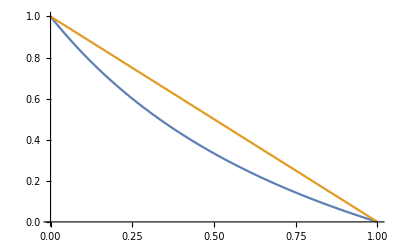

```mathematica
Plot[{(1-x)/(1+x),1-x},{x,0,1}]
```

```mathematica
eqsE = {2 k1 EE S - (k1m + kp) C1 - k2 C1 S + (2k2m + 2kq) C2==0,0==k2 C1 S - (2k2m + 2 kq)C2}
ss=Solve[eqsE/.{EE->E0-C1-C2},{C1,C2}]
ss/.{k2-> (k2m +kq)/Kmp,k1-> (k1m +kp)/Km}//Simplify
```

{-C1 (k1m+kp)+C2 (2 k2m+2 kq)+2 EE k1 S-C1 k2 S==0,0==-C2 (2 k2m+2 kq)+C1 k2 S}

{{C1→(2 E0 k1 (k2m+kq) S)/(k1m k2m+k2m kp+k1m kq+kp kq+2 k1 k2m S+2 k1 kq S+k1 k2 S^2),C2→(E0 k1 k2 S^2)/(k1m k2m+k2m kp+k1m kq+kp kq+2 k1 k2m S+2 k1 kq S+k1 k2 S^2)}}

{{C1→(2 E0 Kmp S)/(Km Kmp+S (2 Kmp+S)),C2→(E0 S^2)/(Km Kmp+S (2 Kmp+S))}}

(1+ⅇ^y)/(-1+ⅇ^y)

ⅇ^y/(-1+ⅇ^y)-(ⅇ^y (1+ⅇ^y))/((-1+ⅇ^y)^2)

(2 ⅇ^y (1+ⅇ^y))/((-1+ⅇ^y)^3)

2+2/(-1+ⅇ^y)

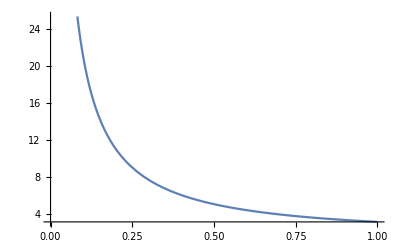

```mathematica
f=(1+Exp[y])/(Exp[y]-1)
fp=D[f,y]
fpp=D[fp,y]//Simplify
1-fpp/fp // FullSimplify
Plot[1-fpp/fp ,{y,0,1}]
```

```mathematica
ps={a1->1,b1->2,c1->1.5,
a2->1,b2->3,c2->1,
a3->2,b3->1,c3->1.5,
a4->3,b4->2,c4->3.5,
x2->3,x5->0,z4->3};
F/.ps
ContourPlot3D[50==(F/.ps),{z1,3,5},{z2,4,6},{z3,2,4}]
```

-(19.75+6.5 z1+6.75 z2+6.5 z1 z2-5.5 z3+3 z1 z3+7.5 z2 z3+3 z1 z2 z3)/((2-z1) (10-3 z2) (1-z3))

-Graphics3D-

```mathematica
F/.ps/.{z1->4,z2->4,z3->3}
```

53.7813

```mathematica
Zs={z1->4,z2->4,z3->3}
D[F/.ps,z3]/.Zs//FullSimplify
```

{z1→4,z2→4,z3→3}

-16.3281

```mathematica
Integrate[1/(x(x-1)^2),x]
```

-1/(-1+x)-Log[-1+x]+Log[x]